## Packages import and definitions

```mathematica
Get[NotebookDirectory[]<>"../Mathematica_packages/QMB.wl"]
```

```mathematica
Get[NotebookDirectory[]<>"../Mathematica_packages/Chaometer.wl"]
```

```mathematica
?Superoperator
```

```mathematica
?QubitChannelSuperoperator
```

## Plots

```mathematica
specialPointsCoord=Join[#,-#]&[IdentityMatrix[3]];
```

```mathematica
specialPointsColors={Magenta,Orange,Red,Blue,Cyan,Green}
```

{RGBColor[1, 0, 1],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[0, 1, 0]}

```mathematica
specialPoints={#[[1]],PointSize[0.02],Point[#[[2]]]}&/@Transpose[{specialPointsColors,specialPointsCoord}]
```

{{RGBColor[1, 0, 1],PointSize[0.02],Point[{1,0,0}]},{RGBColor[1, 0.5, 0],PointSize[0.02],Point[{0,1,0}]},{RGBColor[1, 0, 0],PointSize[0.02],Point[{0,0,1}]},{RGBColor[0, 0, 1],PointSize[0.02],Point[{-1,0,0}]},{RGBColor[0, 1, 1],PointSize[0.02],Point[{0,-1,0}]},{RGBColor[0, 1, 0],PointSize[0.02],Point[{0,0,-1}]}}

```mathematica
SpecialPoints[M_,κ_]:={#[[1]],PointSize[0.02],Point[M.#[[2]]+κ]}&/@Transpose[{specialPointsColors,specialPointsCoord}]
```

```mathematica
points=Complement[Flatten[Table[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,Pi/30,Pi-Pi/30,Pi/30},{ϕ,0,2Pi,Pi/30}],1],specialPointsCoord];
```

```mathematica
Graphics3D[{specialPoints,Point/@points}]
```

-Graphics3D-

## Chaotic region

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3][[1]];
```

```mathematica
canonicalStates=Dyad[Normalize[Eigensystem[Pauli[#]][[2,2]]]]&/@{1,2,3}
```

{{{1/2,1/2},{1/2,1/2}},{{1/2,-ⅈ/2},{ⅈ/2,1/2}},{{1,0},{0,0}}}

```mathematica
t=79.2;
```

```mathematica
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L]
```

{{0.489372+0. ⅈ,0.00289564+0.0104131 ⅈ,0.00289564-0.0104131 ⅈ,0.505512+0. ⅈ},{-0.026634+0.00441006 ⅈ,0.0162296+0.0148661 ⅈ,0.0171228+0.0149619 ⅈ,-0.0267961-0.0133353 ⅈ},{-0.026634-0.00441006 ⅈ,0.0171228-0.0149619 ⅈ,0.0162296-0.0148661 ⅈ,-0.0267961+0.0133353 ⅈ},{0.510628+0. ⅈ,-0.00289564-0.0104131 ⅈ,-0.00289564+0.0104131 ⅈ,0.494488+0. ⅈ}}

```mathematica
ClearAll[x,y,z];BlochVector[ArrayReshape[superoperator.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]]
```

{1/2 ((0.0171228-0.0149619 ⅈ) (x-ⅈ y)+(0.0162296-0.0148661 ⅈ) (x+ⅈ y)-(0.0267961-0.0133353 ⅈ) (1-z)-(0.026634+0.00441006 ⅈ) (1+z))+1/2 ((0.0162296+0.0148661 ⅈ) (x-ⅈ y)+(0.0171228+0.0149619 ⅈ) (x+ⅈ y)-(0.0267961+0.0133353 ⅈ) (1-z)-(0.026634-0.00441006 ⅈ) (1+z)),(0.-0.5 ⅈ) ((0.0171228-0.0149619 ⅈ) (x-ⅈ y)+(0.0162296-0.0148661 ⅈ) (x+ⅈ y)-(0.0267961-0.0133353 ⅈ) (1-z)-(0.026634+0.00441006 ⅈ) (1+z))+(0.+0.5 ⅈ) ((0.0162296+0.0148661 ⅈ) (x-ⅈ y)+(0.0171228+0.0149619 ⅈ) (x+ⅈ y)-(0.0267961+0.0133353 ⅈ) (1-z)-(0.026634-0.00441006 ⅈ) (1+z)),1/2 ((0.00289564+0.0104131 ⅈ) (x-ⅈ y)+(0.00289564-0.0104131 ⅈ) (x+ⅈ y)-0.494488 (1-z)-0.510628 (1+z))+1/2 ((0.00289564+0.0104131 ⅈ) (x-ⅈ y)+(0.00289564-0.0104131 ⅈ) (x+ⅈ y)+0.505512 (1-z)+0.489372 (1+z))}

```mathematica
p=RandomPoint[Sphere[]]
```

{0.00713651,0.866455,0.499205}

```mathematica
%122/.Thread[{x,y,z}->p]
```

{-0.0279713+0. ⅈ,-0.00190568+0. ⅈ,0.0144203+0. ⅈ}

```mathematica
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates]
```

{{0.0333525,-0.0000958201,0.000162121},{-0.029828,-0.000893195,-0.0177454},{0.00579128,0.0208263,-0.0161399}}

```mathematica
M.p+κ
```

{-0.0279713,-0.00190568,0.0144203}

```mathematica
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},0.05]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]}]
```

-Graphics3D-

```mathematica
Graphics3D[SpecialPoints[M,κ]]
```

-Graphics3D-

```mathematica
SpecialPoints[M,κ]
```

{{RGBColor[1, 0, 1],PointSize[0.03],Point[{0.0607323,-0.00461858,0.0224542}].{-0.0699079,0.0262156,-0.00703375}},{RGBColor[1, 0.5, 0],PointSize[0.03],Point[{-0.0169941,-0.00876684,0.0115828}].{-0.0699079,0.0262156,-0.00703375}},{RGBColor[1, 0, 0],PointSize[0.03],Point[{-0.0339571,0.0112545,0.0230929}].{-0.0699079,0.0262156,-0.00703375}},{RGBColor[0, 0, 1],PointSize[0.03],Point[{-0.0607323,0.00461858,-0.0224542}].{-0.0699079,0.0262156,-0.00703375}},{RGBColor[0, 1, 1],PointSize[0.03],Point[{0.0169941,0.00876684,-0.0115828}].{-0.0699079,0.0262156,-0.00703375}},{RGBColor[0, 1, 0],PointSize[0.03],Point[{0.0339571,-0.0112545,-0.0230929}].{-0.0699079,0.0262156,-0.00703375}}}

```mathematica
plots=Table[
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Graphics3D[{{Opacity[0.3],Sphere[]},Point[M.#]&/@points}],{t,28,29,0.1}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
{u,σ,v}=SingularValueDecomposition[M]
```

{{{0.537667,-0.672364,0.508764},{-8.0758×10^-6,-0.603408,-0.797433},{0.843157,0.428749,-0.324438}},{{0.991447,0.,0.},{0.,0.724905,0.},{0.,0.,0.719566}},{{0.54833,0.822097,-0.153268},{0.0421447,0.155879,0.986877},{0.835199,-0.547593,0.0508259}}}

```mathematica
{Graphics3D[{{Opacity[0.3],Sphere[]},Point[ConjugateTranspose[v].#]&/@points},ImageSize->400],Graphics3D[{{Opacity[0.3],Sphere[]},Point[σ.ConjugateTranspose[v].#]&/@points},ImageSize->400],Graphics3D[{{Opacity[0.3],Sphere[]},Point[u.σ.ConjugateTranspose[v].#]&/@points},ImageSize->400],Graphics3D[{{Opacity[0.3],Sphere[]},Point[u.σ.ConjugateTranspose[v].#+κ]&/@points},ImageSize->400]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
FockBasis[#,2]&/@Range[0,3]
```

{{{0,0}},{{1,0},{0,1}},{{2,0},{1,1},{0,2}},{{3,0},{2,1},{1,2},{0,3}}}

```mathematica
FockBasis[2,2]
```

{{2,0},{1,1},{0,2}}

## Chaotic region

### Parameters

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3][[1]];
```

```mathematica
canonicalStates=Dyad[Normalize[Eigensystem[Pauli[#]][[2,2]]]]&/@{1,2,3}
```

{{{1/2,1/2},{1/2,1/2}},{{1/2,-ⅈ/2},{ⅈ/2,1/2}},{{1,0},{0,0}}}

### Rotations

```mathematica
t=12;
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
```

```mathematica
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},r]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},ImageSize->400]
```

-Graphics3D-

```mathematica
r=0.08
{u,σ,v}=SingularValueDecomposition[M];
{Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},r]},Point[ConjugateTranspose[v].#]&/@points},ImageSize->400],
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},r]},
Point[σ.ConjugateTranspose[v].#]&/@points},ImageSize->400],
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},r]},
{Red,Arrowheads[0.02],Arrow[{{0,0,0},#}]&/@(Diagonal[σ]*Transpose[u])},
Point[u.σ.ConjugateTranspose[v].#]&/@points},ImageSize->400]}
```

0.08

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SingularValueList[M]
```

{0.0749758,0.0271395,0.00430492}

### Calculations

```mathematica
t=79.2;
```

```mathematica
superoperatorsRegular={};
```

```mathematica
AbsoluteTiming[
Table[
AppendTo[superoperatorsRegular,Superoperator[t,ψ0E,eigVals,eigVecs,L]];,
{t,0,8,0.1}]
]
```

```mathematica
t=0.1;
κ=BlochVector[ArrayReshape[superoperatorsRegular[[IntegerPart[t/0.1+1]]].{1/2,0,0,1/2},{2,2}]]
SingularValueList[M=Transpose[BlochVector[ArrayReshape[superoperatorsRegular[[IntegerPart[t/0.1+1]]].Flatten[#],{2,2}]]-κ&/@canonicalStates]]
EulerAngles[Transpose[SingularValueDecomposition[M][[1]]]]
```

{0,0,0}

{1.,0.981882,0.981882}

{-3.04059,1.57778,-0.108929}

#### Rotations

```mathematica
Graphics3D[{{Opacity[0.5],Sphere[]},
Table[
M=Transpose[BlochVector[ArrayReshape[superoperatorsRegular[[IntegerPart[t/0.1+1]]].Flatten[#],{2,2}]]-κ&/@canonicalStates];
Point[SingularValueDecomposition[M][[1,1]]],
{t,0,1,0.1}]}
]
```

-Graphics3D-

```mathematica
RotationMatrix[-0.10892901956230555,{0,0,1}].RotationMatrix[1.577781160956333,{0,1,0}].RotationMatrix[-3.040585910893037,{0,0,1}].{0,0,1}
```

{0.994049,-0.108711,-0.00698478}

```mathematica
SingularValueDecomposition[M][[1]]
```

{{-0.819021,0.159101,0.551264},{-0.00597964,0.958366,-0.285479},{-0.573733,-0.23711,-0.783971}}

```mathematica
eulerAngles=Transpose[Table[
M=Transpose[BlochVector[ArrayReshape[i.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Mod[EulerAngles[Transpose[SingularValueDecomposition[M][[1]]]],2Pi]
,{i,superoperatorsRegular[[2;;58]]}]]
```

{{3.2426,3.34544,3.45095,3.55894,3.66375,2.53475,2.49723,2.51868,2.5713,2.61328,2.62644,3.66199,3.67813,2.56582,2.49444,2.3862,2.46644,3.65847,0.408783,0.360477,0.349088,0.345216,0.266443,6.11431,0.388482,0.402952,0.449031,3.6216,3.65036,3.70136,2.49716,3.90403,4.03055,4.08671,2.45133,2.54237,2.6665,2.85615,0.0570957,2.988,0.00268456,3.25275,2.69619,2.45112,2.39466,2.40503,2.44348,2.48199,3.79199,3.8209,3.86913,3.90499,3.90328,3.8491,3.74568,3.62667,3.53349},{1.57778,1.58973,1.59268,1.57023,1.50156,1.77578,1.97663,2.19477,2.37447,2.4975,2.56617,0.560646,0.602886,2.43572,2.25419,1.86337,1.36581,1.94879,2.02234,2.06441,2.09619,2.119,2.12848,2.12585,1.02197,1.03839,1.08035,1.09232,1.08423,1.08053,2.04754,1.13881,1.22149,1.15842,2.41607,2.45526,2.45938,2.45957,0.690649,0.699195,2.48173,0.555417,0.613476,0.78688,0.91799,0.983716,0.993894,0.980433,2.16687,2.15594,2.13829,2.13754,2.17221,2.24146,2.32541,2.40302,2.47183},{6.17426,6.09916,6.05805,6.05227,6.08343,3.00751,3.09233,3.16192,3.1733,3.09521,2.91889,5.80439,5.51135,2.079,1.78259,1.34086,0.8366,3.7658,3.69924,3.72034,3.77256,3.83033,3.88763,3.92492,0.770041,0.653586,0.416258,0.246356,0.129566,0.0118901,3.0132,5.98524,5.80098,5.74778,2.9718,2.97278,2.97808,3.04314,0.00579635,0.117181,3.38166,0.55922,1.06382,1.25171,1.2592,1.1924,1.08337,0.974659,4.05897,4.06626,4.10529,4.12546,4.09471,4.00382,3.86653,3.72492,3.61943}}

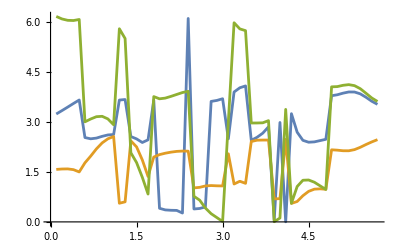

```mathematica
ListPlot[Transpose[{Range[0.1,0.1*57,0.1],#}]&/@eulerAngles,Joined->True]
```

## Superoperators eigenvalues

```mathematica
eigenvalsSuperoperator=Chop[Eigenvalues[#]]&/@superoperatorsRegular;
```

```mathematica
eigenvalsSorted=SortBy[Transpose[{Re[#],Im[#]}],#[[2]]&]&/@eigenvalsSuperoperator;
```

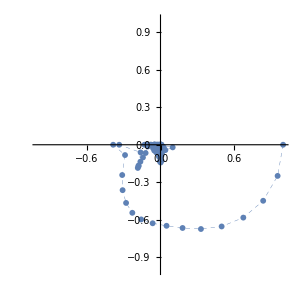
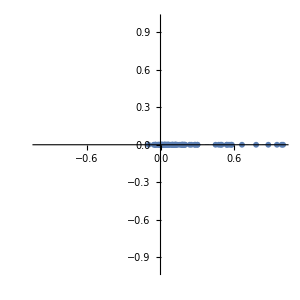
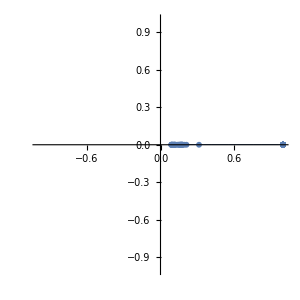
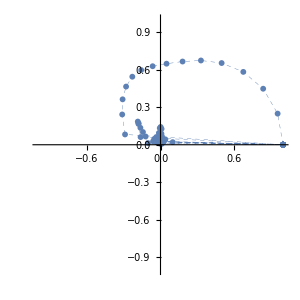

```mathematica
ListLinePlot[eigenvalsSorted[[All,#]],PlotRange->{{-1,1},{-1,1}},PlotMarkers->{Automatic, 6},PlotStyle->Directive[Dashing[0.01],Thickness[0.001]],ImageSize->300,AspectRatio->1]&/@{1,2,3,4}
```

```mathematica
eigvalsU=Table[Eigenvalues[KroneckerProduct[#,Conjugate[#]]&[MatrixExp[-I Pauli[3]t/2]]],{t,0,5,0.05}];
```

```mathematica
eigenvalsUSorted=SortBy[Transpose[{Re[#],Im[#]}],#[[2]]&]&/@eigvalsU;
```

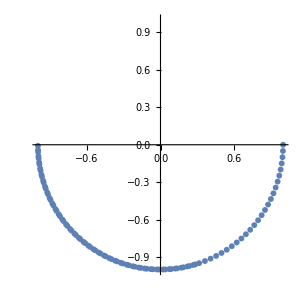
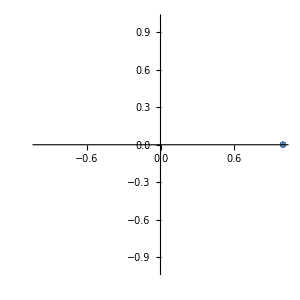
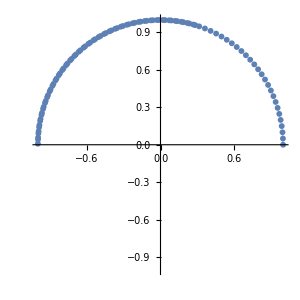
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[eigenvalsUSorted[[All,#]],PlotRange->{{-1,1},{-1,1}},PlotMarkers->{Automatic, 6},PlotStyle->Directive[Dashing[0.01],Thickness[0.001]],ImageSize->300,AspectRatio->1]&/@{1,2,3,4}
```

```mathematica
ClearAll[x,y,z];BlochVector[ArrayReshape[superoperator.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]]
```

{1/2 ((0.0171228-0.0149619 ⅈ) (x-ⅈ y)+(0.0162296-0.0148661 ⅈ) (x+ⅈ y)-(0.0267961-0.0133353 ⅈ) (1-z)-(0.026634+0.00441006 ⅈ) (1+z))+1/2 ((0.0162296+0.0148661 ⅈ) (x-ⅈ y)+(0.0171228+0.0149619 ⅈ) (x+ⅈ y)-(0.0267961+0.0133353 ⅈ) (1-z)-(0.026634-0.00441006 ⅈ) (1+z)),(0.-0.5 ⅈ) ((0.0171228-0.0149619 ⅈ) (x-ⅈ y)+(0.0162296-0.0148661 ⅈ) (x+ⅈ y)-(0.0267961-0.0133353 ⅈ) (1-z)-(0.026634+0.00441006 ⅈ) (1+z))+(0.+0.5 ⅈ) ((0.0162296+0.0148661 ⅈ) (x-ⅈ y)+(0.0171228+0.0149619 ⅈ) (x+ⅈ y)-(0.0267961+0.0133353 ⅈ) (1-z)-(0.026634-0.00441006 ⅈ) (1+z)),1/2 ((0.00289564+0.0104131 ⅈ) (x-ⅈ y)+(0.00289564-0.0104131 ⅈ) (x+ⅈ y)-0.494488 (1-z)-0.510628 (1+z))+1/2 ((0.00289564+0.0104131 ⅈ) (x-ⅈ y)+(0.00289564-0.0104131 ⅈ) (x+ⅈ y)+0.505512 (1-z)+0.489372 (1+z))}

```mathematica
p=RandomPoint[Sphere[]]
```

{0.00713651,0.866455,0.499205}

```mathematica
%122/.Thread[{x,y,z}->p]
```

{-0.0279713+0. ⅈ,-0.00190568+0. ⅈ,0.0144203+0. ⅈ}

```mathematica
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates]
```

{{0.0333525,-0.0000958201,0.000162121},{-0.029828,-0.000893195,-0.0177454},{0.00579128,0.0208263,-0.0161399}}

```mathematica
M.p+κ
```

{-0.0279713,-0.00190568,0.0144203}

```mathematica
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},0.05]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]}]
```

-Graphics3D-

```mathematica
Table[
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},0.11]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},ImageSize->400],{t,46.2,46.5,0.1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},0.11]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},ImageSize->400],{t,79.2,79.5,0.1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{u,σ,v}=SingularValueDecomposition[M]
```

{{{0.537667,-0.672364,0.508764},{-8.0758×10^-6,-0.603408,-0.797433},{0.843157,0.428749,-0.324438}},{{0.991447,0.,0.},{0.,0.724905,0.},{0.,0.,0.719566}},{{0.54833,0.822097,-0.153268},{0.0421447,0.155879,0.986877},{0.835199,-0.547593,0.0508259}}}

```mathematica
{Graphics3D[{{Opacity[0.3],Sphere[]},Point[ConjugateTranspose[v].#]&/@points},ImageSize->400],Graphics3D[{{Opacity[0.3],Sphere[]},Point[σ.ConjugateTranspose[v].#]&/@points},ImageSize->400],Graphics3D[{{Opacity[0.3],Sphere[]},Point[u.σ.ConjugateTranspose[v].#]&/@points},ImageSize->400],Graphics3D[{{Opacity[0.3],Sphere[]},Point[u.σ.ConjugateTranspose[v].#+κ]&/@points},ImageSize->400]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
FockBasis[#,2]&/@Range[0,3]
```

{{{0,0}},{{1,0},{0,1}},{{2,0},{1,1},{0,2}},{{3,0},{2,1},{1,2},{0,3}}}

```mathematica
FockBasis[2,2]
```

{{2,0},{1,1},{0,2}}

## Integrable region

### Parameters

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}
```

{1.,2.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3][[1]];
```

```mathematica
canonicalStates=Dyad[Normalize[Eigensystem[Pauli[#]][[2,2]]]]&/@{1,2,3}
```

{{{1/2,1/2},{1/2,1/2}},{{1/2,-ⅈ/2},{ⅈ/2,1/2}},{{1,0},{0,0}}}

### Calculations

```mathematica
t=79.1;
```

```mathematica
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L]
```

{{0.87606+0. ⅈ,0.2099+0.0335931 ⅈ,0.2099-0.0335931 ⅈ,0.136427+0. ⅈ},{0.197748+0.0182364 ⅈ,0.0771848-0.0531455 ⅈ,0.116238-0.00886759 ⅈ,-0.198648-0.00768516 ⅈ},{0.197748-0.0182364 ⅈ,0.116238+0.00886759 ⅈ,0.0771848+0.0531455 ⅈ,-0.198648+0.00768516 ⅈ},{0.12394+0. ⅈ,-0.2099-0.0335931 ⅈ,-0.2099+0.0335931 ⅈ,0.863573+0. ⅈ}}

```mathematica
p=RandomPoint[Sphere[]];
ClearAll[x,y,z];BlochVector[ArrayReshape[superoperator.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]]/.Thread[{x,y,z}->p]
```

{0.114393+0. ⅈ,0.0139369+0. ⅈ,0.367218+0. ⅈ}

```mathematica
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]]
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates]
```

{-0.000900785,-0.0105513,0.0124874}

{{0.193423,-0.0442779,0.396396},{0.0620131,-0.039053,-0.0259216},{0.4198,0.0671861,0.739634}}

```mathematica
M.p+κ
```

{0.114393,0.0139369,0.367218}

```mathematica
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]}]
```

-Graphics3D-

```mathematica
Table[
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},ImageSize->400],{t,46.2,46.5,0.1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},ImageSize->400],{t,79.2,79.5,0.1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{u,σ,v}=SingularValueDecomposition[M]
```

{{{-0.496369,0.867437,0.034223},{-0.0163304,0.0300852,-0.999414},{-0.867958,-0.496637,-0.000767786}},{{0.971682,0.,0.},{0.,0.107275,0.},{0.,0.,0.102656}},{{-0.521042,0.798963,-0.300288},{-0.015159,-0.360425,-0.932665},{-0.853396,-0.481406,0.199908}}}

```mathematica
v//Eigensystem
```

{{1.,-0.84078+0.541378 ⅈ,-0.84078-0.541378 ⅈ},{{0.416769+0. ⅈ,0.510834+0. ⅈ,-0.751899+0. ⅈ},{0.642769+0. ⅈ,-0.165612+0.58489 ⅈ,0.243764+0.39737 ⅈ},{0.642769+0. ⅈ,-0.165612-0.58489 ⅈ,0.243764-0.39737 ⅈ}}}

```mathematica
ArcCos[0.8407795518152912]/Degree
```

32.7775

```mathematica
32.77/180
```

0.182056

```mathematica
t=89.6;
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},ImageSize->400]
```

-Graphics3D-

```mathematica
t=0.1;
superoperator=Superoperator[t,ψ0E,eigVals,eigVecs,L];
κ=BlochVector[ArrayReshape[superoperator.{1/2,0,0,1/2},{2,2}]];
M=Transpose[BlochVector[ArrayReshape[superoperator.Flatten[#],{2,2}]]-κ&/@canonicalStates];
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},ImageSize->400]

{u,σ,v}=SingularValueDecomposition[M];
{Graphics3D[{{Opacity[0.3],Sphere[]},Point[ConjugateTranspose[v].#]&/@points},ImageSize->400],
Graphics3D[{{Opacity[0.3],Sphere[]},
Point[σ.ConjugateTranspose[v].#]&/@points},ImageSize->400],
Graphics3D[{{Opacity[0.3],Sphere[]},
{Red,Arrow[{{0,0,0},#}]&/@(Diagonal[σ]*Transpose[u])},
Point[u.σ.ConjugateTranspose[v].#]&/@points},ImageSize->400],Graphics3D[{{Opacity[0.3],Sphere[]},Point[u.σ.ConjugateTranspose[v].#+κ]&/@points},ImageSize->400]}
```

-Graphics3D-

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Survival probability

```mathematica
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2
```

### Parameters

```mathematica
L=11(*number of spins*);
(*chaotic region*)
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
SeedRandom[1323];
ψ0=RandomChainProductState[L];
```

```mathematica
(*time points*)
numberOftemporalPoints=500;
tValues=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
AbsoluteTiming[
Module[{ψt},
sp=Table[
ψt=StateEvolution[t,ψ0,eigVals,eigVecs];
{t,SurvivalProbability[ψ0,ψt]},
{t,tValues}];
]
]
```

{81.113,Null}

```mathematica
ipr=Total[Abs[Conjugate[eigVecs].ψ0]^4]
```

0.00104983

```mathematica
numberOftemporalPoints=500;
tValues=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

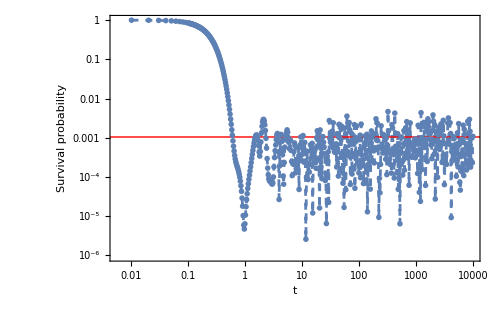

```mathematica
ListLogLogPlot[sp,
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","Survival probability"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500,
Epilog->{Red,InfiniteLine[{1,Log[ipr]},{1,0}]}]
```

```mathematica
Total[Abs[Conjugate[eigVecs].ψ0]^4]
```

0.00407137

```mathematica
Line[{{10^-4,ipr},{100,ipr}}]
```

Line[{{1/10000,0.00407137},{100,0.00407137}}]